```mathematica
50/3*5.5/2
```

45.8333

```mathematica
.360μm(1+(z/(((.360μm)^2*π)/(461nm)))^2)^(1/2)/.z-> 22mm
```

0.36 √(1+(6.20494×10^8 mm^2 nm^2)/μm^4) μm

```mathematica
pos
```

pos

List all elements in the optical path, dimensions all in mm. For a lens, the format is {“Lens”, position along beam path (mm), focal length (mm)}

```mathematica
elements={{"Lens",22,22},{"Lens",645+22,400},{"Lens",645+22+557,146.1},{"Lens",645+22+557+922,1000}};(* demag imaging path 181003*)


(*elementsz = {{"Lens",75,75},{"Lens",370,300}}(*consider two transverse driections separately*)
elementsx = {{"Lens",400,1000},{"Lens",450,-150}}*)

freespace={};
zmax=5000;
λ=461*10^-6;
inputparms={w0->500μm,R0->10^7};(*input waist and curvature in mm*)
lim = 5;
```

```mathematica
lensMatrix[f_]:={{1,0},{-1/f,1}}
freeMatrix[d_]:={{1,d},{0,1}}
matrix[optic_]:=If[optic[[1]]=="Lens",lensMatrix[optic[[3]]],IdentityMatrix[2]]

abcd[z_,optics_]:=Module[{},
elem=Sort[Select[optics,#[[2]]≤z &],#1[[2]]>#2[[2]] &];
matrixlist=If[Length[elem]≥1,
Flatten[Join[{{freeMatrix[z-First[elem][[2]]]},Flatten[Table[{matrix[elem[[ii]]],freeMatrix[elem[[ii,2]]-elem[[ii+1,2]]]},{ii,1,Length[elem]-1}],1],{matrix[Last[elem]]},{freeMatrix[Last[elem][[2]]]}}],1],{freeMatrix[z]}];
orderlist=Reverse[matrixlist];
fullMatrix=IdentityMatrix[2];
For[ii=1,ii≤Length[orderlist],ii++,
fullMatrix=orderlist[[ii]].fullMatrix];
fullMatrix
]
```

```mathematica
q0recip=1/R0-ⅈ λ/(π w0^2)/.inputparms;
z0=(π w0^2)/λ/.inputparms;
qrecip[z_,optics_]:=(abcd[z,optics][[2,1]]+abcd[z,optics][[2,2]]*q0recip)/(abcd[z,optics][[1,1]]+abcd[z,optics][[1,2]]*q0recip)
rcurv[z_,optics_]:=(Re[qrecip[z,optics]])^-1
waist[z_,optics_]:=(-(Im[qrecip[z,optics]]*π)/λ)^(-1/2)
```

## Plot waist

```mathematica
elements
```

{{Lens,22,22},{Lens,667,400},{Lens,1224,146.1},{Lens,2146,1000}}

```mathematica
pos1
```

pos1

```mathematica
xx
```

xx

```mathematica
elements
```

{{Lens,22,22},{Lens,667,400},{Lens,1224,146.1},{Lens,2146,1000}}

```mathematica
waist[z,elements]
```

(√(461/π))/(1000 √(-Im[(1/10000000-(1844 ⅈ)/π)/(1+(1/10000000-(1844 ⅈ)/π) z)]))

```mathematica
645+22+557+922+540
```

2686

```mathematica
elements
```

{{Lens,22,22},{Lens,667,400},{Lens,1224,146.1},{Lens,2146,1000}}

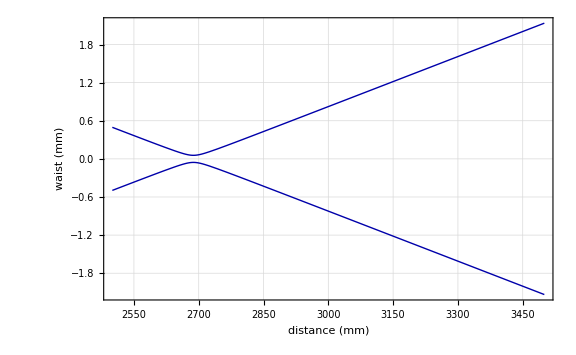

```mathematica
Plot[{waist[z,elements],-waist[z,elements]},{z,2500,3500},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Blue]}},Frame->True, GridLines->Automatic,ImageSize->Large,FrameLabel->{"distance (mm)","waist (mm)"}, PlotRange-> All]
```

### Making interpolating function in region of interest. Expect camera to focus at 645+22+557+922+540 = 2686 mm

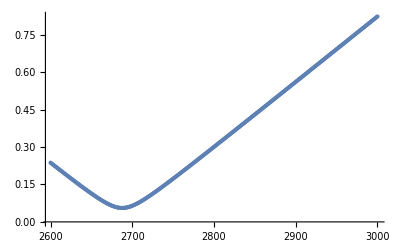

```mathematica
simData = Table[{z,waist[z,elements]},{z,2600,3000}];
ListPlot[simData]
nSimData = Interpolation[simData];
```

```mathematica
Chop[dz[100]]//N
```

Real[(-32856.6+0.458565 ⅈ) Im'[0.01-6.97829×10^-8 ⅈ]]

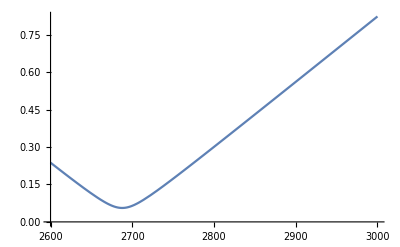

```mathematica
Plot[nSimData[z], {z,2600,3000}]
```

#### Computing magnification

```mathematica
zsub = FindRoot[nSimData[z],{z,2650}]
imagedWaist = nSimData[z]/.zsub
waist[0,elements]//N
Print["Magnification is ",imagedWaist/waist[0,elements]]
```

InterpolatingFunction::dmval: Input value {29574.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5376.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4032.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{z→2687.69}

0.0558338

0.0005

Magnification is 111.668